```mathematica
MitchellNetravali[B_,C_]:=
Function[{x},1/6*Piecewise[
{
{(12-9B-6C)*Abs[x]^3+(-18+12B+6C)*Abs[x]^2+(6-2B), Abs[x]<1},
{(-B-6C)*Abs[x]^3+(6B+30C)*Abs[x]^2+(-12B-48C)*Abs[x]+(8B+24C),1<=Abs[x]<2}
},
0
]
]
```

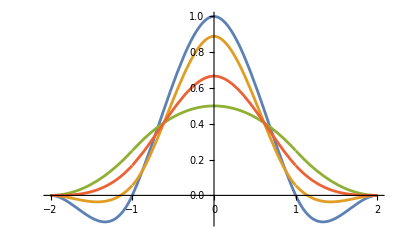

```mathematica
Plot[{
MitchellNetravali[0,1][x],
MitchellNetravali[1/3,1/3][x],
MitchellNetravali[3/2,-1/4][x],
MitchellNetravali[1,0][x]
},{x,-2,2}]
```

```mathematica
Plot3D[Evaluate[MitchellNetravali[0,1][x]*MitchellNetravali[0,1][y]],{x,-2,2},{y,-2,2},PlotRange->Full,Exclusions->{{0,0}}]
```

-Graphics3D-

```mathematica
Plot3D[MitchellNetravali[0,1][Sqrt[x^2+y^2]],{x,-2,2},{y,-2,2},PlotRange->Full,Exclusions->{{0,0}}]
```

-Graphics3D-